```mathematica
SetDirectory[NotebookDirectory[]];
```

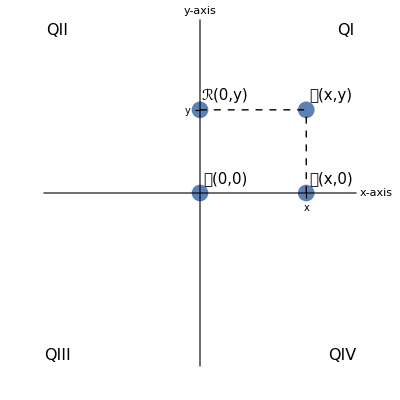

{coordinateplane.svg,coordinateplane.pdf}

```mathematica
a=4.25;b=3;
xmin=-6;xmax=6;
ymin=-6;ymax=6;
Show[ListPlot[{{0,0},{a,b},{a,0},{0,b}},PlotStyle->{PointSize[0.03]}],
Graphics[{Dashed,Line[{{a,0},{a,b}}]}],
Graphics[{Dashed,Line[{{0,b},{a,b}}]}],
PlotRange->{{xmin,xmax},{ymin,ymax}},GridLines->{None},AspectRatio->1,
Ticks->{{{a,HoldForm[x]}},{{b,HoldForm[y]}}},
AxesStyle->Directive[16],
AxesLabel->{"x-axis","y-axis"},
Epilog->{
Text[Style[HoldForm[TraditionalForm[𝒫[x,y]]],15],{a+1,b+0.5}],Text[Style[HoldForm[TraditionalForm[𝒪[0,0]]],15],{1,0.5}],Text[Style[HoldForm[TraditionalForm[𝒬[x,0]]],15],{a+1,0.5}],Text[Style[HoldForm[TraditionalForm[ℛ[0,y]]],15],{1,b+0.5}],

Text[Style[HoldForm[TraditionalForm["QI"]],16],{xmax-0.15,ymax-0.15}],
Text[Style[HoldForm[TraditionalForm["QII"]],16],{xmin+0.3,ymax-0.15}],
Text[Style[HoldForm[TraditionalForm["QIII"]],16],{xmin+0.3,ymin+0.15}],
Text[Style[HoldForm[TraditionalForm["QIV"]],16],{xmax-0.3,ymin+0.15}],
}]
Export[{"coordinateplane.svg","coordinateplane.pdf"},%]
```

```mathematica
<m>P(-3,5)</m>, <m>\mathcal{Q}(2,-4)</m>, <m>\mathcal{R}(-1.5,-2.5)</m>,and<m>\mathcal{S}(0,4)
```

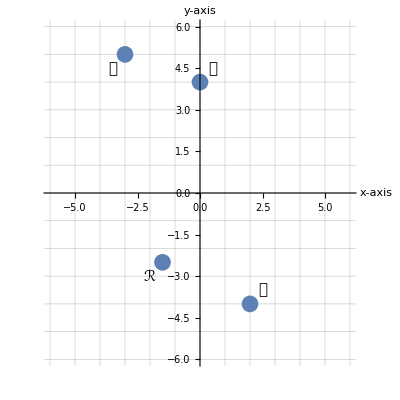

{coordinateplane2.svg,coordinateplane2.pdf}

```mathematica
p={-3,5};
q={2,-4};
r={-1.5,-2.5};
s={0,4};
xmin=-6;xmax=6;
ymin=-6;ymax=6;
Show[ListPlot[{p,q,r,s},PlotStyle->{PointSize[0.03]}],PlotRange->{{xmin,xmax},{ymin,ymax}},GridLines->{Range[xmin,xmax],Range[ymin,ymax]},AxesStyle->Directive[16],
AxesLabel->{"x-axis","y-axis"},AspectRatio->1,
Epilog->{
Text[Style[HoldForm[TraditionalForm[𝒫]],15],p-{0.5,0.5}],Text[Style[HoldForm[TraditionalForm[𝒬]],15],q+{0.5,0.5}],Text[Style[HoldForm[TraditionalForm[ℛ]],15],r-{0.5,0.5}],Text[Style[HoldForm[TraditionalForm[𝒮]],15],s+{0.5,0.5}]}
]
Export[{"coordinateplane2.svg","coordinateplane2.pdf"},%]
```

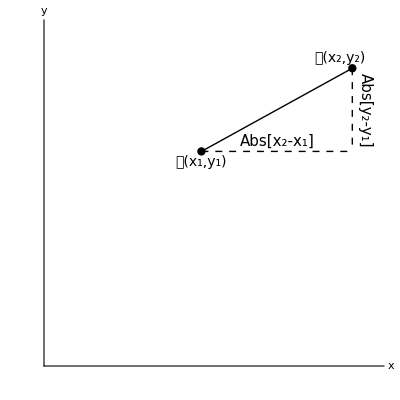

{distance.svg,distance.pdf}

```mathematica
p={1,3};q={4,5};
Show[
Graphics[{Line[{p,q}]}],
Graphics[{Dashed,Line[{p,{q[[1]],p[[2]]}}]}],
Graphics[{Dashed,Line[{q,{q[[1]],p[[2]]}}]}],
ListPlot[{p,q},PlotStyle->{PointSize[0.015],Black}],
Axes->True,AxesLabel->{x,HoldForm[y]},AxesStyle->Directive[ 12],Ticks->None,PlotRange->{{-2,4.5},{-2,6}},AspectRatio->1,
AxesStyle->Directive[16],
AxesLabel->{"x-axis","y-axis"},
Epilog->{
Text[Style[TraditionalForm[HoldForm[𝒫[Subscript[x, 1],Subscript[y, 1]]]],14],p-{0,.25}],Text[Style[TraditionalForm[HoldForm[𝒬[Subscript[x, 2],Subscript[y, 2]]]],14],q+{-0.25,.25}],
Text[Style[TraditionalForm[HoldForm[Abs[Subscript[x, 2]-Subscript[x, 1]]]],15],p+{1.5,0.25}],
Text[Style[Rotate[TraditionalForm[HoldForm[Abs[Subscript[y, 2]-Subscript[y, 1]]]],-Pi/2],15],q+{+0.25,-1}]
}]
Export[{"distance.svg","distance.pdf"},%]
```

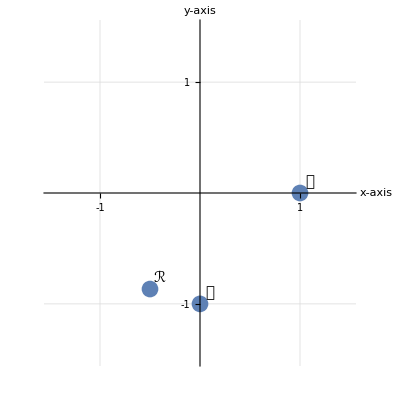

{graphing1.svg,graphing1.pdf}

```mathematica
p={1,0};
q={0,-1};
r={-1/2,-Sqrt[3]/2};
s={0,4};
xmin=-1.5;xmax=1.5;
ymin=-1.5;ymax=1.5;
Show[ListPlot[{p,q,r,s},PlotStyle->{PointSize[0.03]}],PlotRange->{{xmin,xmax},{ymin,ymax}},AxesStyle->Directive[16],
AxesLabel->{"x-axis","y-axis"},AspectRatio->1,GridLines->Automatic,
Ticks->{{-1,1},{-1,1}},
Epilog->{
Text[Style[HoldForm[TraditionalForm[𝒫]],15],p+{0.1,0.1}],Text[Style[HoldForm[TraditionalForm[𝒬]],15],q+{0.1,0.1}],Text[Style[HoldForm[TraditionalForm[ℛ]],15],r+{0.1,0.1}]}
]
Export[{"graphing1.svg","graphing1.pdf"},%]
```

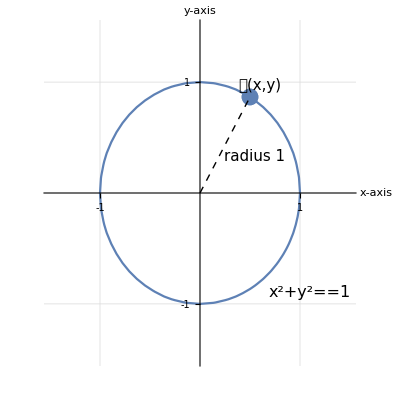

{graphing2.svg,graphing2.pdf}

```mathematica
q={0,-1};
r={-1/2,-Sqrt[3]/2};
s={0,4};
xmin=-1.5;xmax=1.5;
ymin=-1.5;ymax=1.5;
Show[ListPlot[{-r},PlotStyle->{PointSize[0.03]}],
ContourPlot[x^2+y^2==1,{x,-2,2},{y,-2,2}],
Graphics[{Dashed,Line[{{0,0},-r}]}],
PlotRange->{{xmin,xmax},{ymin,ymax}},AxesStyle->Directive[16],
AxesLabel->{"x-axis","y-axis"},AspectRatio->1,
Ticks->{{-1,1},{-1,1}},GridLines->Automatic,
Epilog->{
Text[Style[HoldForm[TraditionalForm[𝒫[x,y]]],15],-r+{0.1,0.1}],Text[Style["radius 1",15],-r/2+{0.3,-0.1}],Text[Style[HoldForm[TraditionalForm[x^2+y^2==1]],16],{1.1,-0.9}]}
]
Export[{"graphing2.svg","graphing2.pdf"},%]
```

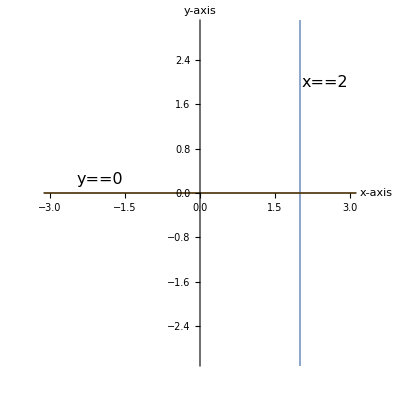

{graphing3.svg,graphing3.pdf}

```mathematica
p={2,4};
Show[ListPlot[{p},PlotStyle->{PointSize[0.03]}],
ContourPlot[{x==2,y==0},{x,-4,4},{y,-4,4},ContourStyle->{{Thick}}],
PlotRange->{{-3,3},{-3,3}},AxesStyle->Directive[16],
AxesLabel->{"x-axis","y-axis"},AspectRatio->1,
Epilog->{Text[Style[HoldForm[TraditionalForm[x==2]],16],{2.5,2}],Text[Style[HoldForm[TraditionalForm[y==0]],16],{-2,0.25}]}
]
Export[{"graphing3.svg","graphing3.pdf"},%]
```

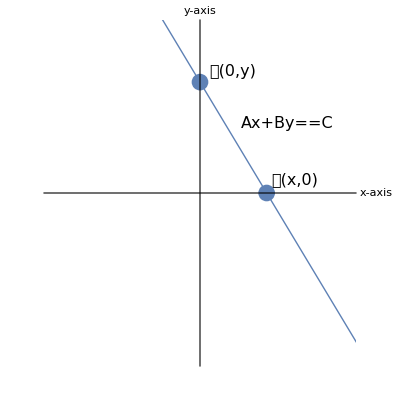

{lines1.svg,lines1.pdf}

```mathematica
p={2,4};
Show[ListPlot[{{0,2},{1+1/3,0}},PlotStyle->{PointSize[0.03]}],
Plot[-3x/2 +2,{x,-4,4},PlotStyle->Thick],
PlotRange->{{-3,3},{-3,3}},AxesStyle->Directive[16],
AxesLabel->{"x-axis","y-axis"},AspectRatio->1,Ticks->None,
Epilog->{Text[Style[HoldForm[TraditionalForm[Ax+By==C]],16],{1.75,1.25}],Text[Style[HoldForm[TraditionalForm[𝒫[x,0]]],16],{1.9,0.25}],
Text[Style[HoldForm[TraditionalForm[𝒬[0,y]]],16],{0.65,2.2}]}
]
Export[{"lines1.svg","lines1.pdf"},%]
```

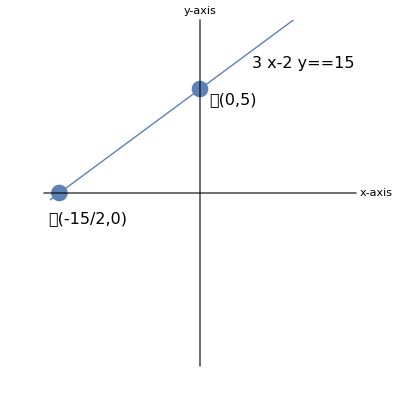

{lines2.svg,lines2.pdf}

```mathematica
Show[ListPlot[{{-15/2,0},{0,5}},PlotStyle->{PointSize[0.03]}],
Plot[2x/3 +5,{x,-8,8},PlotStyle->Thick],
PlotRange->{{-8,8},{-8,8}},AxesStyle->Directive[16],
AxesLabel->{"x-axis","y-axis"},AspectRatio->1,Ticks->None,
Epilog->{Text[Style[HoldForm[TraditionalForm[3x-2y==15]],16],{5.5,6.25}],Text[Style[HoldForm[TraditionalForm[𝒫[-15/2,0]]],16],{-6,-1.25}],
Text[Style[HoldForm[TraditionalForm[𝒬[0,5]]],16],{1.75,4.5}]}
]
Export[{"lines2.svg","lines2.pdf"},%]
```

FittedModel[39.7353+4.54437 x]

39.7353+4.54437 x

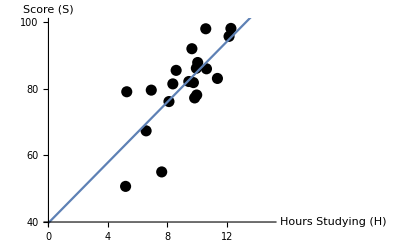

{lines3.svg,lines3.pdf}

```mathematica
data={{5.265016948068337,79.15809653238199},{5.1860755658839714,50.7128463577318},{7.614654587130973,55.05959866173527},{6.566678650758068,67.40922998547168},{6.913182087772338,79.64770852675085},{11.36176770771761,83.16438999356345},{9.746106374939517,81.91596285459048},{9.96833932925652,78.18734566062797},{8.362272508765615,81.52813360784454},{10.0342155102276,87.95244603641552},{8.585930159945761,85.59053720688127},{8.102698244249758,76.2139213946133},{10.577344306373067,98.09514949842911},{9.829687620822257,77.30363327528609},{9.644530256650796,92.09810057992559},{9.437521849070743,82.24044023601353},{12.14290437264471,95.81673267872503},{10.62523968072048,86.06277089427209},{12.2677679371957,98.19959242701322},{9.944675845963086,86.22798510738042}};
model=LinearModelFit[data,x,x]
model["BestFit"]
Show[ListPlot[data,PlotStyle->{Black,PointSize[0.02]}],Plot[model["BestFit"],{x,0,20}],PlotRange->{{0,15},{40,100}},AxesOrigin->{0,40},AxesLabel->{"Hours\nStudying (H)","Score (S)"},AxesStyle->Directive[ 16],Ticks->{Range[0,12,2],{40,60,80,100}}]
Export[{"lines3.svg","lines3.pdf"},%]
```

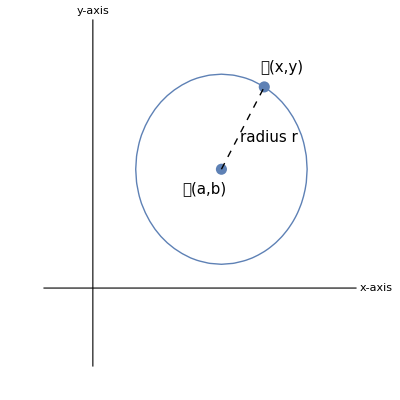

{circle.svg,circle.pdf}

```mathematica
q={0,-1};
r={-1/2,-Sqrt[3]/2};
s={0,4};
xmin=-2;xmax=1.5;
ymin=-2;ymax=1.5;
Show[ListPlot[{{0,0},-r},PlotStyle->{PointSize[0.02]}],
ContourPlot[x^2+y^2==1,{x,-2,2},{y,-2,2},ContourStyle->{Thick}],
Graphics[{Dashed,Line[{{0,0},-r}]}],
PlotRange->{{xmin,xmax},{ymin,ymax}},AxesStyle->Directive[16],
AxesLabel->{"x-axis","y-axis"},AspectRatio->1,
Ticks->None,
AxesOrigin->{-1.5,-1.25},
Epilog->{
Text[Style[HoldForm[TraditionalForm[𝒫[x,y]]],15],-r+{0.2,0.2}],
Text[Style[HoldForm[TraditionalForm[𝒞[a,b]]],15],{-0.2,-0.2}],Text[Style["radius r",15],-r/2+{0.3,-0.1}]}
]
Export[{"circle.svg","circle.pdf"},%]
```

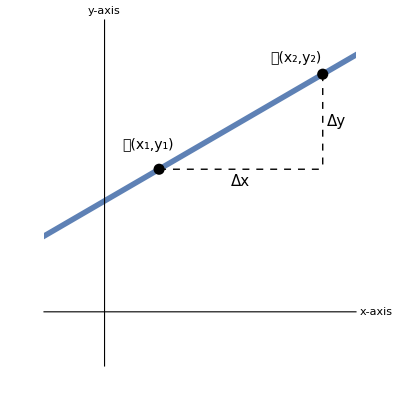

{slope.svg,slope.pdf}

```mathematica
p={1,3};q={4,5};
Show[
Plot[(2/3)(x-1)+3,{x,-5,5},PlotStyle->Thickness[0.01]],
Graphics[{Dashed,Line[{p,{q[[1]],p[[2]]}}]}],
Graphics[{Dashed,Line[{q,{q[[1]],p[[2]]}}]}],
ListPlot[{p,q},PlotStyle->{PointSize[0.02],Black}],
Axes->True,Ticks->None,PlotRange->{{-1,4.5},{-1,6}},AspectRatio->1,
AxesStyle->Directive[16],
AxesLabel->{"x-axis","y-axis"},
Epilog->{
Text[Style[TraditionalForm[HoldForm[𝒫[Subscript[x, 1],Subscript[y, 1]]]],14],p+{-0.2,.5}],Text[Style[TraditionalForm[HoldForm[𝒬[Subscript[x, 2],Subscript[y, 2]]]],14],q+{-0.5,.35}],
Text[Style[TraditionalForm[HoldForm[Δx]],15],p+{1.5,-0.25}],
Text[Style[Rotate[TraditionalForm[HoldForm[Δy]],0],15],q+{+0.25,-1}]
}]
Export[{"slope.svg","slope.pdf"},%]
```

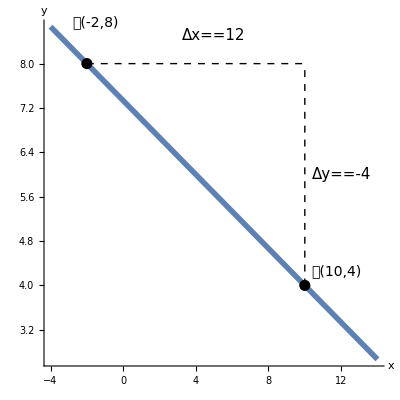

{slope2.svg,slope2.pdf}

```mathematica
p={-2,8};q={10,4};
Show[
Plot[-(1/3)(x+2)+8,{x,-4,14},PlotStyle->Thickness[0.01],PlotRange->All],
Graphics[{Dashed,Line[{p,{q[[1]],p[[2]]}}]}],
Graphics[{Dashed,Line[{q,{q[[1]],p[[2]]}}]}],
ListPlot[{p,q},PlotStyle->{PointSize[0.02],Black}],
Axes->True,AspectRatio->1,
AxesStyle->Directive[16],
AxesLabel->{"x","y"},AxesOrigin->{0,0},
Epilog->{
Text[Style[TraditionalForm[HoldForm[𝒫[-2,8]]],14],p+{0.5,.75}],Text[Style[TraditionalForm[HoldForm[𝒬[10,4]]],14],q+{1.75,.25}],
Text[Style[TraditionalForm[HoldForm[Δx==12]],15],p+{7,+0.5}],
Text[Style[Rotate[TraditionalForm[HoldForm[Δy==-4]],0],15],{12,6}]
}]
Export[{"slope2.svg","slope2.pdf"},%]
```

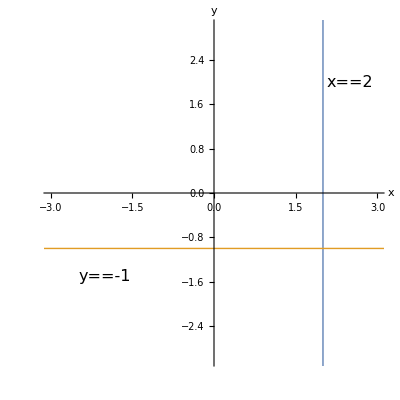

{horizvert.svg,horizvert.pdf}

```mathematica
p={2,4};
Show[ListPlot[{p},PlotStyle->{PointSize[0.03]}],
ContourPlot[{x==2,y==-1},{x,-4,4},{y,-4,4},ContourStyle->{{Thick}}],
PlotRange->{{-3,3},{-3,3}},AxesStyle->Directive[16],
AxesLabel->{"x","y"},AspectRatio->1,
Epilog->{Text[Style[HoldForm[TraditionalForm[x==2]],16],{2.5,2}],Text[Style[HoldForm[TraditionalForm[y==-1]],16],{-2,-1.5}]}
]
Export[{"horizvert.svg","horizvert.pdf"},%]
```

```mathematica
p={2,4};
Show[ListPlot[{p},PlotStyle->{PointSize[0.03]}],
ContourPlot[{x==2,y==-1},{x,-4,4},{y,-4,4},ContourStyle->{{Thick}}],
PlotRange->{{-3,3},{-3,3}},AxesStyle->Directive[16],
AxesLabel->{"x","y"},AspectRatio->1,
Epilog->{Text[Style[HoldForm[TraditionalForm[x==2]],16],{2.5,2}],Text[Style[HoldForm[TraditionalForm[y==-1]],16],{-2,-1.5}]}
]
Export[{"horizvert.svg","horizvert.pdf"},%]
```

-Graphics-

{horizvert.svg,horizvert.pdf}

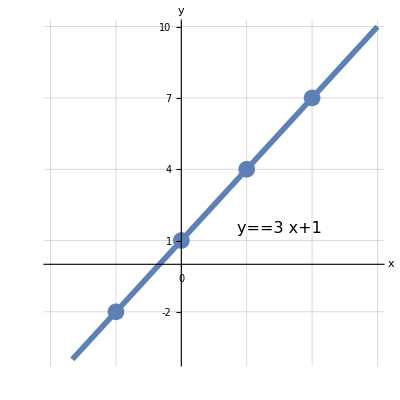

{slopeint.svg,slopeint.pdf}

```mathematica
p={0,3};q={10,4};
Show[
Plot[3x+1,{x,-2,14},PlotStyle->Thickness[0.01],PlotRange->{{-2,3},{-4,10}}],
ListPlot[{{0,1},{1,4},{2,7},{-1,-2}},PlotStyle->PointSize[0.03]],
Axes->True,AspectRatio->1,GridLines->{Range[-10,10],{-6+1,-3+1,0+1,3+1,6+1,9+1}},
Ticks->{Range[-10,10],{-6+1,-3+1,0+1,3+1,6+1,9+1}},
AxesStyle->Directive[16],
AxesLabel->{"x","y"},AxesOrigin->{0,0},
Epilog->{
Text[Style[TraditionalForm[HoldForm[y==3x+1]],16],{1.5,1.5}]
}]
Export[{"slopeint.svg","slopeint.pdf"},%]
```

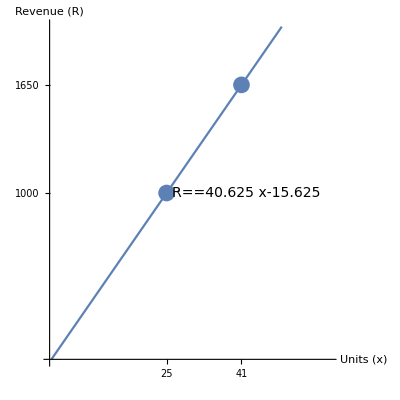

{revenue.svg,revenue.pdf}

```mathematica
p={25,1000};q={41,1650};
Show[
Plot[40.625x-15.625,{x,0,50},PlotRange->{{0,60},{0,2000}},AxesOrigin->{0,0}],
ListPlot[{p,q},PlotStyle->PointSize[0.03]],
Axes->True,AspectRatio->1,Ticks->{{25,41},{1000,1650}},
AxesStyle->Directive[16],
AxesLabel->{"Units\n(x)","Revenue\n(R)"},
Epilog->{
Text[Style[TraditionalForm[HoldForm[R==40.625x-15.625]],14],{42,1000}]
}]
Export[{"revenue.svg","revenue.pdf"},%]
```